```mathematica
Clear[eqs,θ1,θ2,L12,signal,fs,ps,g,width,m1,m2,L,k,tm,initial1,initial2,average,len,s,sample]
```

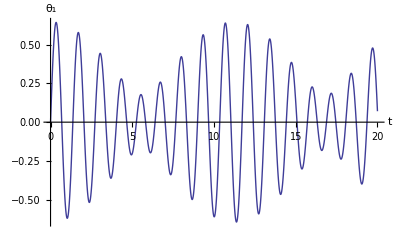

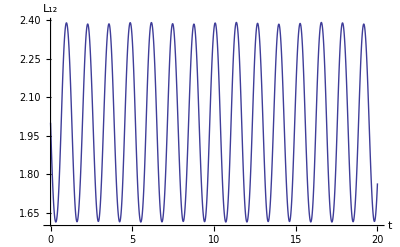

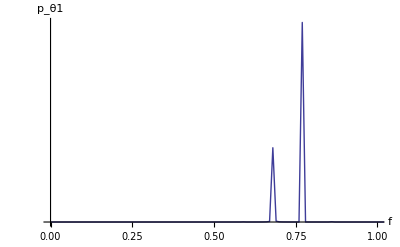

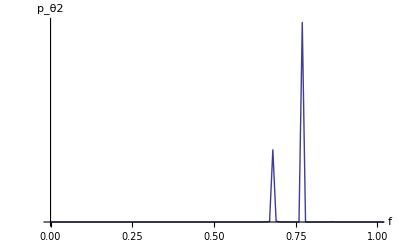

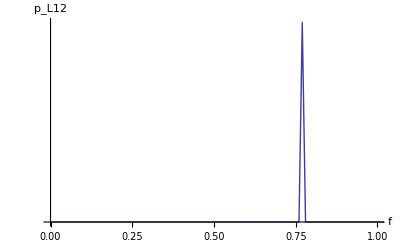

```mathematica
g=9.8;width=2;m1=0.2;m2=0.2;L=0.5;k=0.5;tm=100.0;
initial1={0,1.5/L};initial2={0,-0.5/L};
L12=√((width+L(Sin[θ2[t]]-Sin[θ1[t]]))^2+L^2(Cos[θ2[t]]-Cos[θ1[t]])^2);
eqs={θ1''[t]==1/(m1 L)k(width Cos[θ1[t]]+L Sin[θ2[t]-θ1[t]])(1-width/L12)-g/L Sin[θ1[t]],θ2''[t]==1/(m2 L)-k(width Cos[θ2[t]]+L Sin[θ2[t]-θ1[t]])(1-width/L12)-g/L Sin[θ2[t]],θ1[0]==initial1[[1]],θ1'[0]==initial1[[2]],θ2[0]==initial2[[1]],θ2'[0]==initial2[[2]]};
s=NDSolve[eqs,{θ1,θ2},{t,0,tm},MaxSteps->∞];
{θ1,θ2}={θ1,θ2}/.s[[1]];

Plot[θ1[t],{t,0,tm/5},AxesLabel->{"t","θ_1"}]
Plot[L12,{t,0,tm/5},AxesLabel->{"t","L_12"}]

sample=2000;
signal=Table[θ1[t],{t,0,tm,tm/sample}];
fs=Fourier[signal];ps=(Abs[fs])^2;
len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,1,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,1,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},Ticks->{Automatic,None},AxesLabel->{"f","p_θ1"}]

signal=Table[θ2[t],{t,0,tm,tm/sample}];
fs=Fourier[signal];ps=(Abs[fs])^2;
len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,1,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,1,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},Ticks->{Automatic,None},AxesLabel->{"f","p_θ2"}]

average=Sum[L12,{t,0.0,tm,tm/sample}]/sample;
signal=Table[(L12-average),{t,0.0,tm,tm/sample}];
fs=Fourier[signal];ps=(Abs[fs])^2;
len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,1,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,1,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},Ticks->{Automatic,None},AxesLabel->{"f","p_L12"}]
```